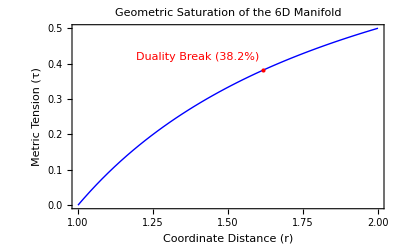

```mathematica
(*COSAT Duality Saturation Plot*)criticalValue=1-1/GoldenRatio;
Plot[1-1/x,{x,1,2},PlotStyle->{Thick,Blue},GridLines->{{1.618},{criticalValue}},Frame->True,FrameLabel->{"Coordinate Distance (r)","Metric Tension (τ)"},PlotLabel->"Geometric Saturation of the 6D Manifold",Epilog->{Red,PointSize[Large],Point[{1.618,criticalValue}],Text["Duality Break (38.2%)",{1.4,0.42}]}]
```

```mathematica
(*Nexus Density Flow Simulation*)VectorPlot3D[{-x/(x^2+y^2+z^2+0.5),-y,-z},{x,-2,2},{y,-2,2},{z,-2,2},VectorStyle->"Arrowhead",VectorPoints->Fine,PlotLabel->"Heisenberg Pressure Gradient at Relativistic Velocity"]
```

-Graphics3D-

```mathematica
(*6D Complex Metric Flavor Gradient*)ComplexPlot3D[(z^2-1)/(z^2+1),{z,-2-2 I,2+2 I},PlotLabel->"6D Phase-Lag Manifold: Real vs Imaginary Potentials",PlotLegends->Automatic]
```

-Graphics3D-